```mathematica
SetDirectory[NotebookDirectory[]];
<<CIP`CurveFit`
```

SetDelayed::write: Tag EdgeChromaticNumber in EdgeChromaticNumber[g_Graph] is Protected.

## Datenimport

Die importierten Daten haben einen Header: “Zeit”,”Temperatur T1”,”Temperatur T2”,”Temperatur T3”,”Temperatur T4”, worauf die Messdaten ab der 4. Zeile folgen.

```mathematica
rawDataMeasurement1=Import["C:\\Users\\martin\\github_repos\\THERMO-EDA\\v1\\data\\Gruppe_3_Messung_1.tsv"];
rawDataMeasurement2=Import["C:\\Users\\martin\\github_repos\\THERMO-EDA\\v1\\data\\Gruppe_3_Messung_2.tsv"];
```

```mathematica
rawDataMeasurement1T=Transpose[Drop[rawDataMeasurement1,{1,3}]];
rawDataMeasurement2T=Transpose[Drop[rawDataMeasurement2,{1,3}]];
```

## Bestimmung der Gefrierpunkterniedrigung

Die Gefrierpunkterniedrigung wird im folgenden Code mit fpd abgekürzt.

```mathematica
convertCelsiusToKelvin[aTemperatureInCelsius_]:=Module[
{},
tmpTemperatureInKelvin=aTemperatureInCelsius+273.15;
tmpTemperatureInKelvin
]
freezingPointDepression[aListOfTemperatures_,theBeginOfConstantRegion_,theEndOfConstantRegion_]:=Module[
{},
tmpListOfConstantTemperatureRegion=Take[aListOfTemperatures,{theBeginOfConstantRegion,theEndOfConstantRegion}];
tmpMeanOfConstantTemperatureRegion=convertCelsiusToKelvin[Mean[tmpListOfConstantTemperatureRegion]];
tmpSdOfConstantTemperatureRegion=StandardDeviation[tmpListOfConstantTemperatureRegion];
tmpAroundObject=Around[tmpMeanOfConstantTemperatureRegion,tmpSdOfConstantTemperatureRegion];
{tmpAroundObject,tmpMeanOfConstantTemperatureRegion,tmpSdOfConstantTemperatureRegion}
]
```

```mathematica
(*Diese beiden Zeilen dienen des Belegs für den gewählten konstanten Bereich.*)
Take[rawDataMeasurement1T[[3]],{625,Length[rawDataMeasurement1T[[3]]]}];
Take[rawDataMeasurement1T[[5]],{495,Length[rawDataMeasurement1T[[5]]]}];
```

```mathematica
fpdWaterMeasurement1=freezingPointDepression[rawDataMeasurement1T[[5]],495,Length[rawDataMeasurement1T[[5]]]]
fpdSugarMeasurement1=freezingPointDepression[rawDataMeasurement1T[[3]],625,Length[rawDataMeasurement1T[[3]]]]
```

{273.2620.021,273.262,0.0214604}

{272.6130.021,272.613,0.0212824}

```mathematica
deltaT[temperatureWater_,temperatureSugar_]:=temperatureWater-temperatureSugar
sdDeltaT[sTempWater_,sTempSugar_]:=Sqrt[
(D[deltaT[temperatureWater,temperatureSugar],temperatureWater]*sTempWater)^2+
(D[deltaT[temperatureWater,temperatureSugar],temperatureSugar]*sTempSugar)^2
]
```

```mathematica
(*Diese beiden Zeilen dienen des Belegs für den gewählten konstanten Bereich.*)
Take[rawDataMeasurement2T[[3]],{645,Length[rawDataMeasurement2T[[3]]]}];
Take[rawDataMeasurement2T[[5]],{500,690}];
```

```mathematica
fpdWaterMeasurement2=freezingPointDepression[rawDataMeasurement2T[[3]],645,Length[rawDataMeasurement2T[[3]]]]
fpdSugarMeasurement2=freezingPointDepression[rawDataMeasurement2T[[5]],500,690]
sdDeltaT[fpdWaterMeasurement2[[3]],fpdSugarMeasurement2[[3]]]
```

{272.770.20,272.765,0.197376}

{272.4610.022,272.461,0.0219206}

0.19859

Die Gefriererniedrigung von Wasser aus der ersten Messung beträgt: 0.112 +- 0.021 °C und von Zucker Saccharose -0.537 +- 0.021 °C

## Bestimmung der kryoskopischen Konstanten für Saccharose

```mathematica
kryoscopicConstant[m1_,m2_,M1_,deltaTemperature_]:=m2/m1*M1*deltaTemperature*1000
D[kryoscopicConstant[m1,m2,M1,deltaTemperature],m1]
D[kryoscopicConstant[m1,m2,M1,deltaTemperature],m2]
D[kryoscopicConstant[m1,m2,M1,deltaTemperature],M1]
D[kryoscopicConstant[m1,m2,M1,deltaTemperature],deltaTemperature]
sdCryoscopicConstant[sdm1_,sdm2_,sddeltaT_]:=Sqrt[
(D[kryoscopicConstant[m1,m2,M1,deltaTemperature],m1]*sdm1)^2+(D[kryoscopicConstant[m1,m2,M1,deltaTemperature],m2]*sdm2)^2+(D[kryoscopicConstant[m1,m2,M1,deltaTemperature],deltaTemperature]*sddeltaT)^2
]
```

-(1000 deltaTemperature M1 m2)/m1^2

(1000 deltaTemperature M1)/m1

(1000 deltaTemperature m2)/m1

(1000 M1 m2)/m1

```mathematica
massSugar={Around[7.99,0.01],7.99,0.01}
massWater={Around[100.38,0.01],100.38,0.01}
molarMassSaccharose=342.30;
```

```mathematica
cryoscopicConstantSaccharose=kryoscopicConstant[massSugar[[2]],massWater[[2]],molarMassSaccharose,deltaT[fpdWaterMeasurement1[[2]],fpdSugarMeasurement1[[2]]]]
sdCryoscopicConstantSaccharose=sdCryoscopicConstant[
0.01,0.01,sdDeltaT[fpdWaterMeasurement2[[3]],fpdSugarMeasurement2[[3]]]] /.{
M1->molarMassSaccharose,
m1->massWater[[2]],
m2->massSugar[[2]],
deltaTemperature->deltaT[fpdWaterMeasurement1[[2]],fpdSugarMeasurement1[[2]]]}
Around[cryoscopicConstantSaccharose,sdCryoscopicConstantSaccharose]
```

2.78846×10^6

5410.87

2.7880.00510^6

## Bestimmung des Molekulargewichtes

```mathematica
molarMass[m1_,m2_,kryoscopicConstant_,deltaTemperature_]:=m1/m2*kryoscopicConstant/deltaTemperature

D[molarMass[m1,m2,cryoscopicConstant,deltaTemperature],m1]
D[molarMass[m1,m2,cryoscopicConstant,deltaTemperature],m2]
D[molarMass[m1,m2,cryoscopicConstant,deltaTemperature],cryoscopicConstant]
D[molarMass[m1,m2,cryoscopicConstant,deltaTemperature],deltaTemperature]

sdMolarMass[sdm1_,sdm2_,sddeltaT_,aSdCryoscopicConstant_]:=Sqrt[
(D[molarMass[m1,m2,cryoscopicConstant,deltaTemperature],m1]*sdm1)^2+
(D[molarMass[m1,m2,cryoscopicConstant,deltaTemperature],m2]*sdm2)^2+(D[molarMass[m1,m2,cryoscopicConstant,deltaTemperature],cryoscopicConstant]*aSdCryoscopicConstant)^2+
(D[molarMass[m1,m2,cryoscopicConstant,deltaTemperature],deltaTemperature]*sddeltaT)^2
]
```

cryoscopicConstant/(deltaTemperature m2)

-(cryoscopicConstant m1)/(deltaTemperature m2^2)

m1/(deltaTemperature m2)

-(cryoscopicConstant m1)/(deltaTemperature^2 m2)

```mathematica
molarMass[
massSugar[[2]],
massWater[[2]],
kryoscopicConstant[
massSugar[[2]],
massWater[[2]],
molarMassSaccharose,
deltaT[fpdWaterMeasurement2[[2]],fpdSugarMeasurement2[[2]]]
],
deltaT[fpdWaterMeasurement2[[2]],fpdSugarMeasurement2[[2]]
]
]/1000
```

```mathematica
sdMolarMassGlucose=sdMolarMass[
massWater[[2]],massSugar[[2]],
sdDeltaT[fpdWaterMeasurement2[[3]],fpdSugarMeasurement2[[3]]],sdCryoscopicConstantSaccharose] /.{
cryoscopicConstant->cryoscopicConstantSaccharose,
m1->massWater[[2]],
m2->massSugar[[2]],
deltaTemperature->deltaT[fpdWaterMeasurement1[[2]],fpdSugarMeasurement1[[2]]]}
```

7.81764×10^7

```mathematica
plotBasicTemperatureProfiles[aTemperatureList_,xmax_]:=Module[{},
Show[ListPlot[aTemperatureList,PlotRange->{{0,xmax},{-25,25}}]]
]
```

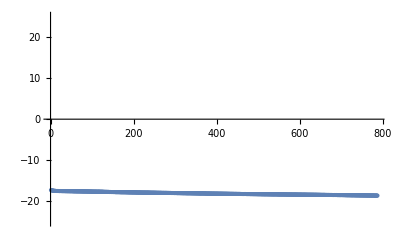
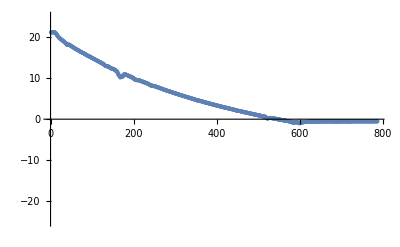
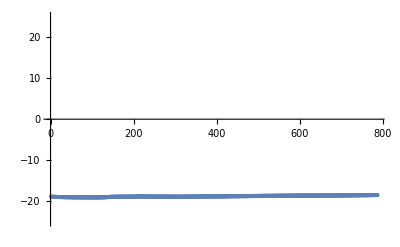
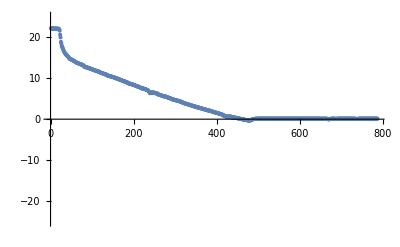

```mathematica
Map[plotBasicTemperatureProfiles[#,Length[rawDataMeasurement1T[[1]]]]&,Drop[rawDataMeasurement1T,1]]
```